## Making Tables

We’ve seen a few ways to make lists in the Wolfram Language. You can just type them in. You can use Range. And you can use functions like IntegerDigits. One of the most common and flexible ways to make lists is with the function Table.

In its very simplest form, Table makes a list with a single element repeated some specified number of times.

Make a list that consists of 5 repeated 10 times:

```mathematica
Table[5,10]
```

{5,5,5,5,5,5,5,5,5,5}

This makes a list with x repeated 10 times:

```mathematica
Table[x,10]
```

{x,x,x,x,x,x,x,x,x,x}

You can repeat lists too:

```mathematica
Table[{1,2},10]
```

{{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2}}

Or, actually, anything; here’s a list of 3 identical pie charts:

```mathematica
Table[PieChart[{1,1,1}],3]
```

{-Graphics-,-Graphics-,-Graphics-}

But what if we want to make a table where the elements aren’t identical? We can do that by introducing a variable, and then iterating over that variable.

Iterate over n to make a list where n goes up to 5:

```mathematica
Table[a[n],{n,5}]
```

{a[1],a[2],a[3],a[4],a[5]}

Here’s how this works. To make the first element of the list, n is taken to be 1, so a[n] is a[1]. To make the second element, n is taken to be 2, so a[n] is a[2], and so on. n is called a variable because it’s varying as we make the different elements of the list.

Make a table that gives the value of n+1 when n goes from 1 to 10:

```mathematica
Table[n+1,{n,10}]
```

{2,3,4,5,6,7,8,9,10,11}

Make a table of the first 10 squares:

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

With Table, you can make tables of anything.

Here’s a table of successively longer lists produced by Range:

```mathematica
Table[Range[n],{n,5}]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

Here each of the lists produced is shown as a column:

```mathematica
Table[Column[Range[n]],{n,8}]
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8}

Here’s a table of plots of successively longer lists of values:

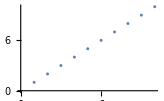
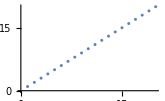
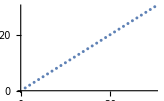

```mathematica
Table[ListPlot[Range[10*n]],{n,3}]
```

Here are pie charts with successively more segments:

```mathematica
Table[PieChart[Table[1,n]],{n,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

So far we’ve always used n as our variable. That’s a pretty common choice. But we can actually use any (lowercase) letter we want, or any combination of letters. All that matters is that wherever the variable appears, its name is the same.

expt is a perfectly good variable name:

```mathematica
Table[2^expt,{expt,10}]
```

{2,4,8,16,32,64,128,256,512,1024}

Here we’re using x as the variable name, and it happens to appear several times:

```mathematica
Table[{x,x+1,x^2},{x,5}]
```

{{1,2,1},{2,3,4},{3,4,9},{4,5,16},{5,6,25}}

In Table[f[n],{n,5}], n takes on values 1, 2, 3, 4, 5. Table[f[n],{n,3,5}] says to start at 3 instead: 3, 4, 5.

This generates a table with n going from 1 to 10:

```mathematica
Table[f[n],{n,10}]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

This generates a table with n going from 4 to 10:

```mathematica
Table[f[n],{n,4,10}]
```

{f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

This makes n go from 4 to 10 in steps of 2:

```mathematica
Table[f[n],{n,4,10,2}]
```

{f[4],f[6],f[8],f[10]}

The Wolfram Language emphasizes consistency, so for example Range is set up to deal with starting points and steps just like Table.

Generate the range of numbers 4 to 10:

```mathematica
Range[4,10]
```

{4,5,6,7,8,9,10}

Generate the range of numbers 4 to 10 going in steps of 2:

```mathematica
Range[4,10,2]
```

{4,6,8,10}

Go from 0 to 1 in steps of 0.1:

```mathematica
Range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

There are usually many ways to do the same thing in the Wolfram Language. For example, here’s how Table and Range can produce identical plots.

Generate a table and plot it:

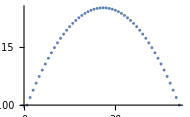

```mathematica
ListPlot[Table[x-x^2,{x,0,1,.02}]]
```

Get the same result by doing arithmetic with the range of values:

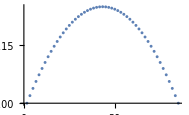

```mathematica
ListPlot[Range[0,1,.02]-Range[0,1,.02]^2]
```

Table always separately computes each entry in the list it generates—and you can see this if you use RandomInteger in Table.

This generates 20 independent random integers with size up to 10:

```mathematica
Table[RandomInteger[10],20]
```

{3,1,4,3,6,7,6,10,9,2,1,4,5,8,3,8,3,8,3,0}

RandomInteger can actually also generate the list directly.

This again generates 20 random integers with size up to 10:

```mathematica
RandomInteger[10,20]
```

{3,0,3,1,9,6,0,8,5,2,7,8,0,10,4,4,9,5,7,1}

Vocabulary

Table[x,5] |   | list of 5 copies of x 
Table[f[n],{n,10}] |   | list of values of f[n] with n going up to 10 
Table[f[n],{n,2,10}] |   | list of values with n going from 2 to 10 
Table[f[n],{n,2,10,4}] |   | list of values with n going from 2 to 10 in steps of 4 
Range[5,10] |   | list of numbers from 5 to 10 
Range[10,20,2] |   | list of numbers from 10 to 20 in steps of 2 
RandomInteger[10,20] |   | list of 20 random integers up to 10

"10 Exercises Available"
"with 11 extras" | "Get Started »"

Make a list in which the number 1000 is repeated 5 times. »

| Expected output: |  
  | {1000,1000,1000,1000,1000} |

Make a table of the values of n^3 for n from 10 to 20. »

| Expected output: |  
  | {1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000} |

Make a number line plot of the first 20 squares. »

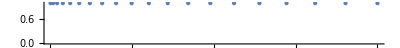
| Expected output: |  
  | -Graphics- |

Make a list of the even numbers (2, 4, 6, ...) up to 20. »

| Expected output: |  
  | {2,4,6,8,10,12,14,16,18,20} |

Use Table to get the same result as Range[10]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10} |

Make a bar chart of the first 10 squares. »

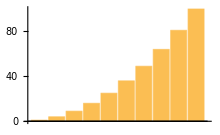
| Expected output: |  
  | -Graphics- |

Make a table of lists of digits for the first 10 squares. »

| Expected output: |  
  | {{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}} |

Make a list line plot of the length of the sequence of digits for each of the first 100 squares. »

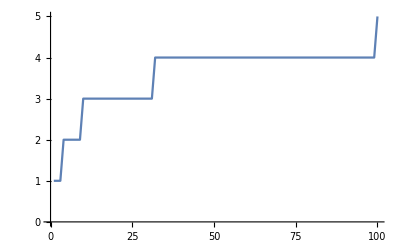
| Expected output: |  
  | -Graphics- |

Make a table of the first digit of the first 20 squares. »

| Expected output: |  
  | {1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4} |

Make a list line plot of the first digits of the first 100 squares. »

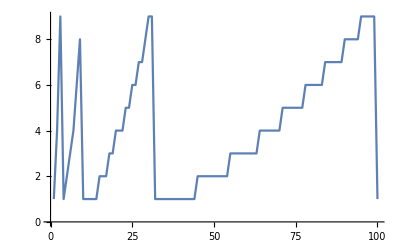
| Expected output: |  
  | -Graphics- |

Make a list of the differences between n^3 and n^2 with n up to 10. »

| Expected output: |  
  | {0,4,18,48,100,180,294,448,648,900} |

Make a list of the odd numbers (1, 3, 5, ...) up to 100. »

| Expected output: |  
  | {1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99} |

Make a list of the squares of even numbers up to 100. »

| Expected output: |  
  | {4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000} |

Create the list {-3,-2,-1,0,1,2} using Range. »

| Expected output: |  
  | {-3,-2,-1,0,1,2} |

Make a list for numbers n up to 20 in which each element is a column of the values of n, n^2 and n^3. »

| Expected output: |  
  | {1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000} |

Make a list line plot of the last digits of the first 100 squares. »

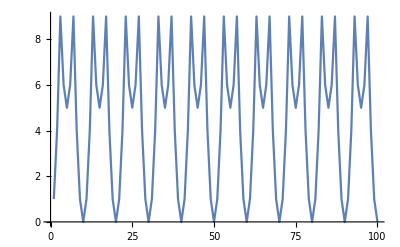
| Expected output: |  
  | -Graphics- |

Make a list line plot of the first digit of the first 100 multiples of 3. »

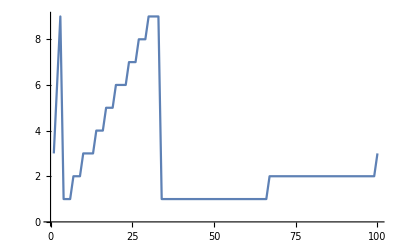
| Expected output: |  
  | -Graphics- |

Make a list line plot of the total of the digits for each number up to 200. »

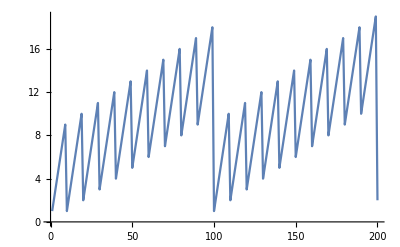
| Expected output: |  
  | -Graphics- |

Make a list line plot of the total of the digits for each of the first 100 squares. »

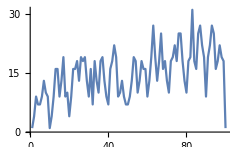
| Expected output: |  
  | -Graphics- |

Make a number line plot of the numbers 1/n with n from 1 to 20. »

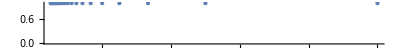
| Expected output: |  
  | -Graphics- |

Make a line plot of a list of random integers where the nth integer is between 0 and n. »

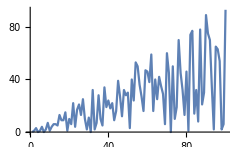
| Expected output: |  
  | -Graphics- |

Q&A

What does the {...} (list) in Table[n^2,{n,5}] mean?

A list is always a way of collecting things together. Here what it’s collecting is the variable n and its range 5. In the Wolfram Language, this kind of use of a list is called an iterator specification.

Why is the {...} (list) in Table[n^2,{n,5}] needed?

So one can easily generalize to multidimensional arrays, like Table[x^2-y^2,{x,5},{y,5}].

What are the constraints on the names of variables?

They can be any sequence of letters or numbers, but they can’t start with a number, and—to avoid possible confusion with built-in Wolfram Language functions—they shouldn’t start with a capital letter.

Why do you have to name a variable if the name never matters?

Good question! In Section 26, we’ll see how to avoid having named variables. It’s very elegant, but it’s a little more abstract than what we’re doing with Table here.

Can Range deal with negative numbers?

Yes. Range[-2,2] gives {-2,-1,0,1,2}. Range[2,-2] gives {}, but Range[2,-2,-1] gives {2,1,0,-1,-2}.

Tech Notes

If you specify steps that don’t fit evenly in the range you give, Range and Table just go as far as the steps take them, potentially stopping before the upper limit. (So Range[1,6,2] gives {1,3,5}, stopping at 5, not 6.)

Using forms like Table[x,20] requires at least Version 10.2 of the Wolfram Language. In earlier versions, this had to be specified as Table[x,{20}].

More to Explore

The Table Function in the Wolfram Language »